## 1. Solving TOV equations.

#### Constants

```mathematica
G = 6.6743 10^-8;
c = 2.99792458 10^10;

Subscript[M, sol]=1.9885 10^33;
α=G Subscript[M, sol]/(10^5 c^2);
Subscript[E0, sol]= Subscript[M, sol] c^2;

mp=1.67262192369 10^-24;
mn=1.67492749804 10^-24;
me = 9.1093837015  10^-28;
c = 2.99792458 10^10;
λp=1.32140985539 10^-13;
λn =2.1001941552  10^-14;
λe = 2.42631023867 10^-10;

km3 = (10.0^5)^3;
rmin = 0.001;
rmax = 350;
densup = 7.86;
```

### 1.1 Equation of state:

#### 1.1.1 Relativistic Case (pure NS)

Let’s try first just this one: relativistic case

```mathematica
Pressure R[ϵ_]:=ϵ/3;
Density R[p_]:=3p;
```

#### 1.1.2 Non Relativistic Case (pure NS)

Pressure and density take the following form

```mathematica
ϵ(P) = 5 (m/(15 π^2 λ^3))^(2/5)P^(3/5)
```

with m, λ of the gas we are considering, let’s say neutrons only, then

```mathematica
kf[m_,l_]:=5((m c^2)/(15 π^2 l^3))^(0.4);
kn=kf[mn,λn];
kp=k[mp,λp];
ke=k[me,λe];

Density NR[p_]:=kn p^0.6
```

#### 1.1.3 Whole Range Neutron Star (Pure NS)

We need first to define density and pressure as function of non-dimensional fermi momentum

```mathematica
nfun[m_,l_]:= (m c^2)/(8 π^2 l^3)
epsilon i[z_,m_,l_]:= nfun[m,l]((2 z^3 + z )Sqrt[1 +z^2] - ArcSinh[z])
pressure i[z_,m_,l_]:=nfun[m,l]((2z^3 /3-z)Sqrt[1+z^2]+ArcSinh[z])
```

now, we create a table of data (p, ϵ):

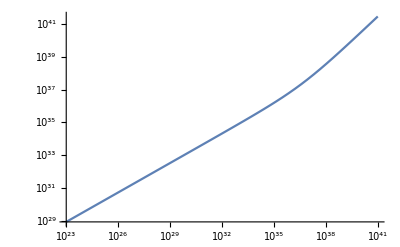

```mathematica
ListEoS n={};Do[ ListEoS n=Union[d,Table[{pressure i[z,mn,λn],epsilon i[z,mn,λn]},{z,10.^i,10^(i+1)-10^(i-1),10^(i-2)}]],{i,-3,2}]
EoS n=Interpolation[ListEoS n,InterpolationOrder->100];LogLogPlot[EoS n[x],{x,10^23,10^41}]
```

Now, let’s build the function for the whole range as a piecewise function taking the R and NR approx,

```mathematica
pw=Piecewise[{{Density NR[x], 0≤  x<10^23}, {EoS n[x],10^23≤ x≤ 10^45},{Density R[x],x>10^45}}];
dener n[p_]:=pw/.x-> p
```

Now we can proceed to do the numerical integration

#### Newton Equations:

We solve first this simple case.

```mathematica
Pc = 3.3 10^34;
ListRG={};
Do[
{solutionN = NDSolve[{p'[r]== If[p[r]>0,-(α dener[p[r]*Pc]*M[r])/(Pc r^2),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],p[rmin]==1,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
mass ad[x_]:=M[x]/.solutionN[[1]];
pressure ad[x_]:=p[x]/.solutionN[[1]];
If[pressure ad[rad]==0,
Print["Central Pressure = ", Pc, "\n",
	"Radius in km = ", rad, "\n",
	"Mass in M_s = ", mass ad[rad]];
Break[],
ListRG=Append[ListRG,{rad,dener[Pc*pressure ad[rad]]}]
];
},
{rad,1,15,.1}]
```

Central Pressure = 3.3×10^34
Radius in km = 14.8
Mass in M_s = 0.804711

#### TOV Equations:

```mathematica
ListPc ={10^33,10^38};
ListR = Table[0,Length[ListPc]];
ListM = Table[0,Length[ListPc]];
Listmass =Table[0,Length[ListPc]];
Listϵ={};
Listp={};
Do[{
Pc = ListPc[[ñ]];
localp = {};
localϵ = {};
Do[{ 
solutionTOV = NDSolve[
{p'[r]== If[p[r]>0,-α*(M[r]+(4 π (Pc km3)/Subscript[E0, sol])r^3 p[r] )(dener[p[r]*Pc]/Pc+p[r])/(r(r - 2 α  M[r])),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],
p[rmin]==1.0,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
mass[x_]=M[x]/.solutionTOV[[1]];
TOVpressure[x_]:=p[x]/.solutionTOV[[1]];
If[TOVpressure[rad]==0,
Break[],
localϵ=Append[localϵ,{rad,dener[Pc*TOVpressure[rad]]/Pc}];
localp=Append[localp,{rad,TOVpressure[rad]}];
ListR[[ñ]]=rad;
Listmass[[ñ]]=mass;
ListM[[ñ]]=mass[rad];
];
},{rad,rmin+0.1,15,.1}];
Listϵ = Append[Listϵ, localϵ];
Listp = Append[Listp, localp];
},{ñ,1,Length[ListPc]}]
```

```mathematica
{ListR[[1]],ListM[[1]],Listmass[[1]][10]}
```

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

{14.901,0.243368,0.378704}

```mathematica
PureNSDensity=ListLogPlot[Listϵ,Joined->True,
Frame->True,
PlotStyle->Red,
FrameLabel->{"r [km]","ρ(r) [g / cm^3]"}]
```

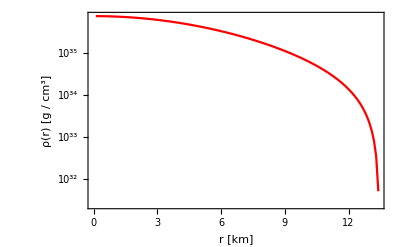

```mathematica
Export["Plots/PureNS_Density.pdf",PureNSDensity];
```

### Gravity Tunnel inside the NS (Pure case)

First, define non dimensional functions for energy density and pressure (they are both in terms of central pressure)

```mathematica
ϵ n=Table[0,Length[ListPc]];
p n=Table[0,Length[ListPc]];
Do[{
ϵ n[[ñ]]= Interpolation[Listϵ[[ñ]],InterpolationOrder->10];
p n[[ñ]] = Interpolation[Listp[[ñ]],InterpolationOrder->10]},{ñ,1,Length[ListPc]}]
```

Along with the non-dimensional mass, this will be useful to define the metric tensor component functions:

```mathematica
Subscript[g, rr](r)=A(r) = (1 - (2 G M(r))/r)^-1 = (1 - 2α (M̄)/r)^-1
```

with M̄ in units of solar masses and r in km. Then

```mathematica
A = Table[0,Length[ListPc]];
Do[{m =Listmass[[ñ]];a[r_]:= (1 - 2 α m[r]/r)^-1; A[[ñ]]=a} ,{ñ,1,Length[ListPc]}]
```

and the other function comes from the diff. eq.

```mathematica
(B'(r))/(B(r))= - (2 P'(r))/(P(r)+ϵ(r))
```

with boundary conditions in the surface equal to the Schwarzschild solution for the exterior metric:

```mathematica
B = Table[0,Length[ListPc]];
Do[{Bmax =1- (2 α)/ListR[[ñ]];
BFunction=NDSolve[ {Bb'[r] == -2 Bb[r] p n[[ñ]]'[r]/(p n[[ñ]][r]+ϵ n[[ñ]][r]),Bb[ListR[[ñ]]]== Bmax},Bb[r],{r,rmin+0.1,ListR[[ñ]]}];
b[r_]=Bb[r]/.BFunction[[1]];
B[[ñ]]=b},{ñ,1,Length[ListPc]}]
```

with  A=g_rr and B=g_tt, we already have all the components of the metric. The general energy diff. eq. is

```mathematica
1/2(dr/dτ)^2+1/2 g^rr(r)(1 - g^tt(r) E^2)c^2=0
```

from this energy-like equation, consider the potential part, at the turning points (r=R),

```mathematica
V(R) = 1/2 g^rr(R)(1 - g^tt(R) E^2)c^2=0
E^2= 1/(g^tt(R))= Subscript[g, tt](R) 
-> E^2 = B(R)
```

we have therefore the following integral:

```mathematica
Δτ = 2/c∫(√(-Subscript[g, tt](r)))/(√(1 - E^2/Subscript[g, rr](r)))ⅆr
Δτ = 2/c(∫_0)^R(√(A(r)B(r)))/(√(B(R)- B(r)))ⅆr
```

```mathematica
A[[1]][ListR[[1]]]
```

InterpolatingFunction::dmval: Input value {14.901} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.08115

```mathematica
τsNS =2 NIntegrate[Sqrt[A[[1]][r] B[[1]][r]/(B[[1]][ListR[[1]]]-B[[1]][r])],{r,rmin,ListR[[1]]}]/(10^(-5) c)
```

InterpolatingFunction::dmval: Input value {14.901} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {14.900999981527585622352317572401929823486255166642422409495338798}. NIntegrate obtained 7.66853 and 0.0000850834 for the integral and error estimates.

0.000051159

```mathematica
τminNS=τsNS/60
```

8.52649×10^-7

## Equation of state npe

```mathematica
Zp[z_,mn_,mp_,me_]:=Sqrt[(mn^2 (1+z^2) - (me^2 + mp^2))^2-4 mp^2 me^2 ]/(2 mp mn Sqrt[1 + z^2])
Ze[z_,mn_,mp_,me_]:=mp/me Zp[z,mn,mp,me]

epsilon pe[z_]:=  epsiloni[z,mp,λp]+epsiloni[938.2/0.511 z, me, λe]
pressure pe[z_]:=pressurei[z,mp,λp]+epsiloni[938.2/0.511z ,me,λe]

epsilon npe[z_]:= epsiloni[z,mn,λn]+ epsiloni[Zp[z,939.5,938.2,0.511],mp,λp]+epsiloni[Ze[z,939.5,938.2,0.511], me, λe]
pressure npe[z_]:=pressurei[z,mn,λn]+pressurei[Zp[z,939.5,938.2,0.511],mp,λp]+epsiloni[Ze[z,939.5,938.2,0.511],me,λe]
```

Non relativistic regime (before z_critical=Zc)

```mathematica
Zc=Zp[0,939.5,938.2,0.511]
```

0.00127321

```mathematica
{pressure pe[Zc],pressure npe[0]}
```

{5.03337×10^22,5.03337×10^22}

```mathematica
eosNR1=Table[{pressure pe[z],epsilon pe[z]},{z,0,Zc,10^-6}];
```

```mathematica
eos0 =Table[{pressure npe[z],epsilon npe[z]},{z,0,10^-3,10^-6 }];
eos1 =Table[{pressure npe[z],epsilon npe[z]},{z,10^-3,10^-2,10^-5}];
eos2=Table[{pressure npe[z],epsilon npe[z]},{z,10.^-2,10^-1,10^-4}];
eos3=Table[{pressure npe[z],epsilon npe[z]},{z,10.^-1,10^0,10^-3}];
eos4=Table[{pressure npe[z],epsilon npe[z]},{z,10.^0,10^1,10^-2}];
eos5=Table[{pressure npe[z],epsilon npe[z]},{z,10.^1,10^2,10^-1}];
eos6=Table[{pressure npe[z],epsilon npe[z]},{z,10.^2,10^3,10^0}];
```

```mathematica
eos npe=Union[eosNR1,eos0,eos1,eos2,eos3,eos4,eos5,eos6];
EOS NS = Interpolation[eos npe,InterpolationOrder->6];
```

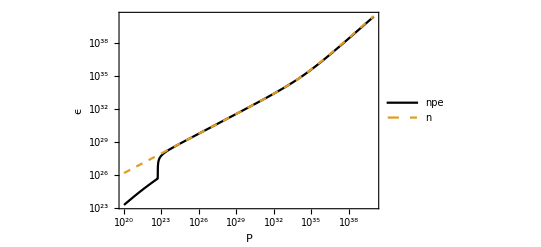

```mathematica
LogLogPlot[{EOS NS[x],dener[x]},{x,10^20,10^40},
Frame->True,
FrameLabel->{"P ","ϵ"},
PlotStyle->{Black,Dashed},
PlotLegends->Placed[{"npe", "n"},{Left,Top}]]
```